```mathematica
Integrate[x^2,{x,0,1}]
```

1/3

```mathematica
Integrate[x^2*1/x,{x,0,1}]
```

1/2

```mathematica
2*Integrate[x*(1-x)*1/x,{x,0,1}]
```

1

```mathematica
-x*D[x^2,x]+1/2*x*(1-x)*D[x^2,{x,2}]//FullSimplify
```

x-3 x^2

```mathematica
-x*D[x*(1-x),x]+1/2*x*(1-x)*D[x*(1-x),{x,2}]
```

-(1-2 x) x-(1-x) x

```mathematica
DSolve[{D[f[t],t]==-f[t],f[0]==x0},f,t]
```

{{f→Function[{t},ⅇ^-t x0]}}

```mathematica
DSolve[{D[f[t],t]==x0*Exp[-t]-3*f[t],f[0]==x0^2},f,t]
```

{{f→Function[{t},1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)]}}

```mathematica
1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)//FullSimplify
```

```mathematica
pHom = 1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)
```

1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)

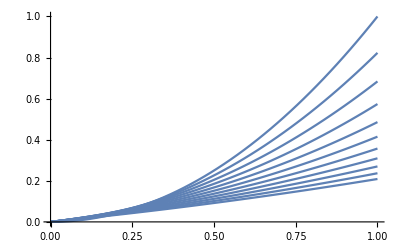

```mathematica
Plot[Table[1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0),{t,0,1,.1}],{x0,0,1}]
```

```mathematica
pHet = 2*(x0*Exp[-t]-pHom)//FullSimplify
```

ⅇ^(-3 t) (1+ⅇ^(2 t)-2 x0) x0

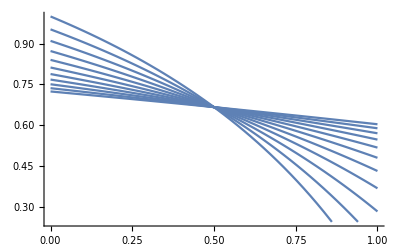

```mathematica
Plot[Table[pHet/(pHet+pHom),{t,0,1,.1}],{x0,0,1}]
```

```mathematica
pHetgHetHom = pHet/(pHet+pHom)//FullSimplify
```

1/(3/2+(-1+2 x0)/(1+ⅇ^(2 t)-2 x0))

```mathematica
pHetAncTable = Table[Table[pHetgHetHom,{x0,.01,.99,.01}],{t,0,1,.1}];
```

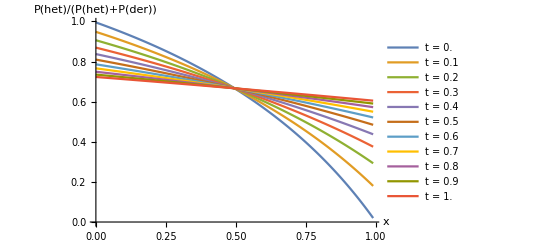

```mathematica
ListLinePlot[pHetAncTable,PlotRange->All,DataRange->{.0,.99},PlotLegends->Table[StringForm["t = ``",ti],{ti,0,1,.1}],AxesLabel->{"x","P(het)/(P(het)+P(der))"}]
```

```mathematica
pHetgHetHom/.{t->.01,x0->.01}
```

0.990051

```mathematica
ExAnc = ⅇ^-t x0/.t->t1
```

ⅇ^-t1 x0

```mathematica
Ex2Anc = 1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)/.t->t1
```

1/2 ⅇ^(-3 t1) x0 (-1+ⅇ^(2 t1)+2 x0)

```mathematica
ExSplit = x0*Exp[-t1]
```

ⅇ^-t1 x0

```mathematica
Ex2Split = (Exp[-t1]-1/2*Exp[-(3*t1+t2)]-1/2*Exp[-(t1+t2)])*x0+Exp[-(3*t1+t2)]*x0^2
```

(ⅇ^-t1-1/2 ⅇ^(-3 t1-t2)-ⅇ^(-t1-t2)/2) x0+ⅇ^(-3 t1-t2) x0^2

```mathematica
pHetgHetHomSplit = 1-Ex2Split/(2*ExSplit-Ex2Split)//FullSimplify
```

1/(1/2+ⅇ^(2 t1+t2)/(1+ⅇ^(2 t1)-2 x0))

```mathematica
pHetgHetHomAnc = 1-Ex2Anc/(2*ExAnc-Ex2Anc)//FullSimplify
```

1/(3/2+(-1+2 x0)/(1+ⅇ^(2 t1)-2 x0))

```mathematica
pHetSplitTable = Table[Table[pHetgHetHomSplit/.t2->t1-.1,{x0,.01,.99,.01}],{t1,.1,1,.1}];
```

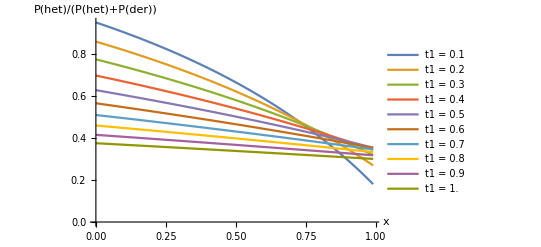

```mathematica
ListLinePlot[pHetSplitTable,PlotRange->All,DataRange->{.0,.99},PlotLegends->Table[StringForm["t1 = ``",ti],{ti,.1,1,.1}],AxesLabel->{"x","P(het)/(P(het)+P(der))"}]
```

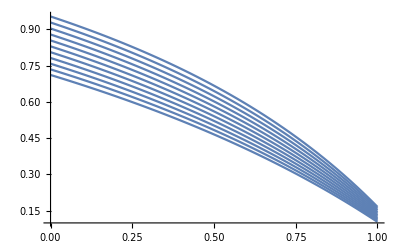

```mathematica
Plot[Table[pHetgHetHomSplit/.t1->0.1,{t2,0,.5,.05}],{x0,0,1}]
```

```mathematica
blah = pHetgHetHomAnc/pHetgHetHomSplit//FullSimplify
```

(1+ⅇ^(2 t1) (1+2 ⅇ^t2)-2 x0)/(1+3 ⅇ^(2 t1)-2 x0)

```mathematica
3*(3-1)/2
```

3

```mathematica
Q = {{0,0,0},{1,-1,0},{0,3,-3}}
```

```mathematica
{{0,0,0},{1,-1,0},{0,3,-3}}//MatrixForm
```

(0 | 0 | 0
1 | -1 | 0
0 | 3 | -3)

```mathematica
MatrixExp[Q*t].{x,x^2,x^3}//FullSimplify
```

{x,x+ⅇ^-t (-1+x) x,1/2 x (2+ⅇ^(-3 t) (-1+x) (-1+3 ⅇ^(2 t)+2 x))}

```mathematica
-3*(3+1)/2
```

-6

```mathematica
Qd = {{-1,0,0},{1,-3,0},{0,3,-6}}
```

{{-1,0,0},{1,-3,0},{0,3,-6}}

```mathematica
Truth = MatrixExp[Q*t2].MatrixExp[Qd*t1].{x,x^2,x^3}
```

{ⅇ^-t1 x,(1/2 ⅇ^(-3 t1-t2) (-1+ⅇ^(2 t1))+ⅇ^(-t1-t2) (-1+ⅇ^t2)) x+ⅇ^(-3 t1-t2) x^2,(1/10 ⅇ^(-6 t1-3 t2) (-1+ⅇ^t1)^2 (2+4 ⅇ^t1+6 ⅇ^(2 t1)+3 ⅇ^(3 t1))+1/2 ⅇ^(-t1-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2)+3/4 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t1)) (-1+ⅇ^(2 t2))) x+(ⅇ^(-6 t1-3 t2) (-1+ⅇ^(3 t1))+3/2 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t2))) x^2+ⅇ^(-6 t1-3 t2) x^3}

```mathematica
(Ex2Split/.x0->x)/((1/2 ⅇ^(-3 t1-t2) (-1+ⅇ^(2 t1))+ⅇ^(-t1-t2) (-1+ⅇ^t2)) x+ⅇ^(-3 t1-t2) x^2)//FullSimplify
```

1

```mathematica
blah  = MatrixExp[Q*t2].MatrixExp[Qd*t1]
```

{{ⅇ^-t1,0,0},{1/2 ⅇ^(-3 t1-t2) (-1+ⅇ^(2 t1))+ⅇ^(-t1-t2) (-1+ⅇ^t2),ⅇ^(-3 t1-t2),0},{1/10 ⅇ^(-6 t1-3 t2) (-1+ⅇ^t1)^2 (2+4 ⅇ^t1+6 ⅇ^(2 t1)+3 ⅇ^(3 t1))+1/2 ⅇ^(-t1-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2)+3/4 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t1)) (-1+ⅇ^(2 t2)),ⅇ^(-6 t1-3 t2) (-1+ⅇ^(3 t1))+3/2 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t2)),ⅇ^(-6 t1-3 t2)}}

```mathematica
Truth2 = blah.{x,x^2,x^3}
```

{ⅇ^-t1 x,(1/2 ⅇ^(-3 t1-t2) (-1+ⅇ^(2 t1))+ⅇ^(-t1-t2) (-1+ⅇ^t2)) x+ⅇ^(-3 t1-t2) x^2,(1/10 ⅇ^(-6 t1-3 t2) (-1+ⅇ^t1)^2 (2+4 ⅇ^t1+6 ⅇ^(2 t1)+3 ⅇ^(3 t1))+1/2 ⅇ^(-t1-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2)+3/4 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t1)) (-1+ⅇ^(2 t2))) x+(ⅇ^(-6 t1-3 t2) (-1+ⅇ^(3 t1))+3/2 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t2))) x^2+ⅇ^(-6 t1-3 t2) x^3}

```mathematica
Truth3 = blah.Table[Beta[k-1/2+i,n-k-1/2]/Beta[k-1/2,n-k-1/2],{i,1,3}]//FullSimplify
```

{(ⅇ^-t1 (-1+2 k))/(2 (-1+n)),(ⅇ^(-3 t1-t2) (-1+2 k) (1+2 k+(-1+ⅇ^(2 t1) (-1+2 ⅇ^t2)) n))/(4 (-1+n) n),(ⅇ^(-3 (2 t1+t2)) (-1+2 k) (4+ⅇ^(3 t1) (5+ⅇ^(2 t1)+20 ⅇ^(2 t1+3 t2)-15 ⅇ^(2 t2) (1+ⅇ^(2 t1)))+(5 (-2+ⅇ^(3 t1) (-1+3 ⅇ^(2 t2))) (1+2 k))/n+(5 (3+4 k (2+k)))/(n (1+n))))/(40 (-1+n))}

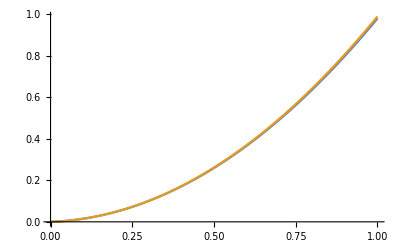

```mathematica
Plot[{Truth[[2]]/.{t1->.01,t2->.05},Truth3[[2]]/.k->x*n/.{n->100,t1->.01,t2->.05}},{x,0,1}]
```

```mathematica
FullSimplify[Beta[k+m,n-k+1]/Beta[k,n-k+1],Assumptions->Element[k,Integers]&&Element[n,Integers]&&Element[m,Integers]&&k>0&&m>0&&n>0]
```

(n! Gamma[k+m])/((m+n)! Gamma[k])

```mathematica
Integrate[x^m*x^(k-1)*(1-x)^(n-k),{x,0,1}]
```

ConditionalExpression[(Gamma[k+m] Gamma[1-k+n])/Gamma[1+m+n],Re[k-n]<1&&Re[k+m]>0]

```mathematica
(* USING THE SAMPLING PROBS EXPLICITLY *)
```

```mathematica
L[f_]:= 1/2*x*(1-x)*D[f,{x,2}]
```

```mathematica
Dmunk= L[x^k*(1-x)^(n-k)]
```

1/2 (1-x) x ((-1+k) k (1-x)^(-k+n) x^(-2+k)-2 k (-k+n) (1-x)^(-1-k+n) x^(-1+k)+(-1-k+n) (-k+n) (1-x)^(-2-k+n) x^k)

```mathematica
Ld [f_]:=-x*D[f,x]+1/2*x*(1-x)*D[f,{x,2}]
```

```mathematica
Ld[x^k*(1-x)^(n-k)]
```

1/2 (1-x) x ((-1+k) k (1-x)^(-k+n) x^(-2+k)-2 k (-k+n) (1-x)^(-1-k+n) x^(-1+k)+(-1-k+n) (-k+n) (1-x)^(-2-k+n) x^k)-x (k (1-x)^(-k+n) x^(-1+k)-(-k+n) (1-x)^(-1-k+n) x^k)

```mathematica
Dμ[n][k] = 1/2 ((-1+k) k μ[n][k-1]-2 k (-k+n) μ[n,k]+(-1-k+n) (-k+n)μ[n][k+1])
```

1/2 (-2 k (-k+n) μ[n,k]+(-1+k) k μ[n][-1+k]+(-1-k+n) (-k+n) μ[n][1+k])

```mathematica
?Piecewise
```

RowBox[{"Piecewise", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a piecewise function with values SubscriptBox[StyleBox["val", "TI"], StyleBox["i", "TI"]] in the regions defined by the conditions SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Piecewise", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["val", "TI"]}], "]"}] uses default value StyleBox["val", "TI"] if none of the SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]] apply. The default for StyleBox["val", "TI"] is 0.

```mathematica
makeMatrix[n_]:=Module[{k,i},Table[Table[Piecewise[{{-k*(n-k),i==k},{1/2*k*(k-1),i==k-1},{1/2*(n-k-1)*(n-k),i==k+1}}],{i,1,n}],{k,1,n}]]
```

```mathematica
makeHet[n_]:= Table[x^k*(1-x)^(n-k),{k,1,n}]
```

```mathematica
L[f_]:= 1/2*x*(1-x)*D[f,{x,2}]
```

```mathematica
Dmunk= L[x^k*(1-x)^(n-k)]
```

1/2 (1-x) x ((-1+k) k (1-x)^(-k+n) x^(-2+k)-2 k (-k+n) (1-x)^(-1-k+n) x^(-1+k)+(-1-k+n) (-k+n) (1-x)^(-2-k+n) x^k)

```mathematica
Ld [f_]:=-x*D[f,x]+1/2*x*(1-x)*D[f,{x,2}]
```

```mathematica
generatorDown = Ld[x^k*(1-x)^(n-k)]
```

1/2 (1-x) x ((-1+k) k (1-x)^(-k+n) x^(-2+k)-2 k (-k+n) (1-x)^(-1-k+n) x^(-1+k)+(-1-k+n) (-k+n) (1-x)^(-2-k+n) x^k)-x (k (1-x)^(-k+n) x^(-1+k)-(-k+n) (1-x)^(-1-k+n) x^k)

```mathematica
Dμ[n][k] = 1/2 ((-1+k) k μ[n][k-1]-2 k (-k+n) μ[n,k]+(-1-k+n) (-k+n)μ[n][k+1])
```

1/2 (-2 k (-k+n) μ[n,k]+(-1+k) k μ[n][-1+k]+(-1-k+n) (-k+n) μ[n][1+k])

```mathematica
?Piecewise
```

RowBox[{"Piecewise", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a piecewise function with values SubscriptBox[StyleBox["val", "TI"], StyleBox["i", "TI"]] in the regions defined by the conditions SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Piecewise", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["val", "TI"]}], "]"}] uses default value StyleBox["val", "TI"] if none of the SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]] apply. The default for StyleBox["val", "TI"] is 0.

```mathematica
makeQ[n_]:=Module[{k,i},Table[Table[Piecewise[{{-k*(n-k),i==k},{1/2*k*(k-1),i==k-1},{1/2*(n-k-1)*(n-k),i==k+1}}],{i,0,n}],{k,0,n}]]
```

```mathematica
makeHet[n_]:= Table[x^k*(1-x)^(n-k),{k,0,n}]
```

```mathematica
makeQd[n_]:=Module[{k,i},Table[Table[Piecewise[{{-k*(n-k+1),i==k},{1/2*k*(k-1),i==k-1},{1/2*(k-n-1)*(k-n),i==k+1}}],{i,0,n}],{k,0,n}]]
```

```mathematica
makeQmu[n_]:=Module[{k,i}, Table[Table[Piecewise[{{k,i==k-1},{-(n-k),i==k}}],{i,0,n}],{k,0,n}]]
```

```mathematica
makeQmuBoth[n_]:=Module[{k,i},Table[Table[Piecewise[{{α/2*k,i==k-1},{-α/2*(n-k)-β/2*k,i==k},{β/2*(n-k),i==k+1}}],{i,0,n}],{k,0,n}]]
```

```mathematica
Q = makeQ[3];
```

```mathematica
Qd = makeQd[3];
```

```mathematica
het = makeHet[3];
```

```mathematica
het/.x->.2
```

{0.512,0.128,0.032,0.008}

```mathematica
-(n-k)-k
```

-n

```mathematica
MatrixExp[Q].MatrixExp[Qd].het/.x->.2
```

{0.904217,0.00757474,0.00705773,0.0518857}

```mathematica
Sum[MatrixExp[Q].MatrixExp[Qd].het
```

```mathematica
makeQd[3]
```

{{0,6,0,0},{0,-3,3,0},{0,1,-4,1},{0,0,3,-3}}

```mathematica
1/2*(1-ϵ)+(1-1/2)*ϵ//FullSimplify
```

1/2

```mathematica
((k-n-1)*(k-n))/((n-k)*(n-k+1))//FullSimplify
```

1

```mathematica
L[n!/(k!*(n-k)!)*x^k(1-x)^(n-k)]
```

((1-x) x ((-1+k) k (1-x)^(-k+n) x^(-2+k)-2 k (-k+n) (1-x)^(-1-k+n) x^(-1+k)+(-1-k+n) (-k+n) (1-x)^(-2-k+n) x^k) n!)/(2 k! (-k+n)!)

```mathematica
FullSimplify[(-1+k) k*n!/(k!*(n-k)!),k≤n&&n>0]
```

((-1+k) k n!)/(k! (-k+n)!)

```mathematica
Q1 = makeQ[3]
```

{{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}}

```mathematica
Q2 = makeQ[4]
```

{{0,6,0,0,0},{0,-3,3,0,0},{0,1,-4,1,0},{0,0,3,-3,0},{0,0,0,6,0}}

```mathematica
h1 = makeHet[3]
```

{(1-x)^3,(1-x)^2 x,(1-x) x^2,x^3}

```mathematica
h2=makeHet[4]
```

{(1-x)^4,(1-x)^3 x,(1-x)^2 x^2,(1-x) x^3,x^4}

```mathematica
p1 = MatrixExp[Q1*t1]
```

{{1,1/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)),1/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1),0},{0,1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),0},{0,1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),0},{0,1/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1),1/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)),1}}

```mathematica
p2 = MatrixExp[Q2*t2]
```

{{1,1/5 ⅇ^(-6 t2) (-1-5 ⅇ^(3 t2)-9 ⅇ^(5 t2)+15 ⅇ^(6 t2)),3+(3 ⅇ^(-6 t2))/5-(18 ⅇ^-t2)/5,1/5 ⅇ^(-6 t2) (-1+ⅇ^t2)^3 (1+3 ⅇ^t2+6 ⅇ^(2 t2)+5 ⅇ^(3 t2)),0},{0,1/10 ⅇ^(-6 t2) (2+5 ⅇ^(3 t2)+3 ⅇ^(5 t2)),3/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),1/10 ⅇ^(-6 t2) (-1+ⅇ^t2)^2 (2+4 ⅇ^t2+6 ⅇ^(2 t2)+3 ⅇ^(3 t2)),0},{0,1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (3+2 ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),0},{0,1/10 ⅇ^(-6 t2) (-1+ⅇ^t2)^2 (2+4 ⅇ^t2+6 ⅇ^(2 t2)+3 ⅇ^(3 t2)),3/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),1/10 ⅇ^(-6 t2) (2+5 ⅇ^(3 t2)+3 ⅇ^(5 t2)),0},{0,1/5 ⅇ^(-6 t2) (-1+ⅇ^t2)^3 (1+3 ⅇ^t2+6 ⅇ^(2 t2)+5 ⅇ^(3 t2)),3+(3 ⅇ^(-6 t2))/5-(18 ⅇ^-t2)/5,1/5 ⅇ^(-6 t2) (-1-5 ⅇ^(3 t2)-9 ⅇ^(5 t2)+15 ⅇ^(6 t2)),1}}

```mathematica
p1.h1//FullSimplify
```

{-1/2 ⅇ^(-3 t1) (-1+x) (2 ⅇ^(3 t1)-3 ⅇ^(2 t1) x+x (-1+2 x)),-1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)-2 x) (-1+x) x,-1/2 ⅇ^(-3 t1) (-1+x) x (-1+ⅇ^(2 t1)+2 x),1/2 x (2+ⅇ^(-3 t1) (-1+x) (-1+3 ⅇ^(2 t1)+2 x))}

```mathematica
p2.h2//FullSimplify
```

{1/5 ⅇ^(-6 t2) (-1+x) (-5 ⅇ^(6 t2)+x+9 ⅇ^(5 t2) x+5 (-1+x) x^2-5 ⅇ^(3 t2) x (-1+2 x)),-1/10 ⅇ^(-6 t2) (-1+x) x (3 ⅇ^(5 t2)+ⅇ^(3 t2) (5-10 x)+2 (1+5 (-1+x) x)),1/5 ⅇ^(-6 t2) (-1+x) x (1-ⅇ^(5 t2)+5 (-1+x) x),-1/10 ⅇ^(-6 t2) (-1+x) x (3 ⅇ^(5 t2)+5 ⅇ^(3 t2) (-1+2 x)+2 (1+5 (-1+x) x)),1/5 ⅇ^(-6 t2) x (5 ⅇ^(6 t2)+9 ⅇ^(5 t2) (-1+x)+5 ⅇ^(3 t2) (-1+x) (-1+2 x)+(-1+x) (1+5 (-1+x) x))}

```mathematica
makeBinom[n1_,n2_]:= Table[Table[Binomial[n2,k2]*Binomial[n1,k1],{k2,0,n2}],{k1,0,n1}]
```

```mathematica
bin = makeBinom[3,4]
```

{{1,4,6,4,1},{3,12,18,12,3},{3,12,18,12,3},{1,4,6,4,1}}

```mathematica
joint = bin*((p1.h1)⊗(p2.h2))//FullSimplify;
```

```mathematica
{{m11,m12,m13},{m21,m22,m23},{m31,m32,m33}}.{v1,v2,v3}
```

{m11 v1+m12 v2+m13 v3,m21 v1+m22 v2+m23 v3,m31 v1+m32 v2+m33 v3}

```mathematica
e1 = {0,1,1/2,0}
```

{0,1,1/2,0}

```mathematica
e2 = {0,1,1/2,1/3,0}
```

{0,1,1/2,1/3,0}

```mathematica
jointEq=bin*(p1.e1)⊗(p2.e2)//FullSimplify;
```

```mathematica
{0,1,0,0}.p1
```

{0,1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),0}

```mathematica
{0,0,1,0,0}.p2
```

{0,1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (3+2 ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),0}

```mathematica
{0,1,0,0}.p1*{0,0,1,0,0}.p2
```

Thread::tdlen: Objects of unequal length in {0,1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),0} {0,1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (3+2 ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),0} cannot be combined.

{0,1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),0} {0,1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (3+2 ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),0}

```mathematica
(jointEq)[[1,2]]
```

1/30 ⅇ^(-3 (t1+2 t2)) (-1+10 ⅇ^(3 t2)+21 ⅇ^(5 t2)) (-1+ⅇ^(2 t1) (-9+10 ⅇ^t1))

```mathematica
D[Exp[(θ*q1+q2)t],θ]
```

ⅇ^(t (q2+q1 θ)) q1 t

```mathematica
θ/2*(1-x)*D[x^k(1-x)^(n-k),x]
```

1/2 (1-x) (k (1-x)^(-k+n) x^(-1+k)-(-k+n) (1-x)^(-1-k+n) x^k) θ

```mathematica
Qmu = makeQmu[3]
```

{{-3,0,0,0},{1,-2,0,0},{0,2,-1,0},{0,0,3,0}}

```mathematica
Qmu+Q
```

{{-3,3,0,0},{1,-4,1,0},{0,3,-3,0},{0,0,6,0}}

```mathematica
Q
```

{{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}}

```mathematica
QmuBoth = makeQmuBoth[3]
```

{{-(3 α)/2,(3 β)/2,0,0},{α/2,-α-β/2,β,0},{0,α,-α/2-β,β/2},{0,0,(3 α)/2,-(3 β)/2}}

```mathematica
test = Table[Binomial[3,i],{i,0,3}]*MatrixExp[(QmuBoth+Q)*t].h1;
```

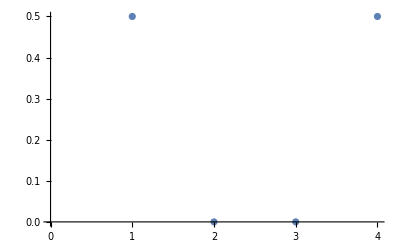

```mathematica
ListPlot[Table[Limit[test[[i]]/.{α->.00001,β->.00001}//FullSimplify,t->∞],{i,1,4}]]
```

```mathematica
testD = β/2*Limit[D[test,β],β->0]
```

$Aborted

```mathematica
blah = Gamma[θ1+θ2]/(Gamma[θ1]*Gamma[θ2])*x^(θ1-1)*(1-x)^(θ2-1)
```

((1-x)^(-1+θ2) x^(-1+θ1) Gamma[θ1+θ2])/(Gamma[θ1] Gamma[θ2])

```mathematica
blah2 = blah/.{θ2->θ,θ1->θ}
```

((1-x)^(-1+θ) x^(-1+θ) Gamma[2 θ])/Gamma[θ]^2

```mathematica
Limit[D[blah2,θ],θ->0]
```

1/(2 x-2 x^2)

```mathematica
Limit[blah+D[blah,θ1],θ1->0]
```

(1-x)^(-1+θ2)/x

```mathematica
MatrixExp[θ/2*Qmu*t].MatrixExp[Q*t]//FullSimplify//MatrixForm
```

(ⅇ^(-(3 t θ)/2) | 1/2 ⅇ^(-3/2 t (2+θ)) (-1+ⅇ^(2 t) (-3+4 ⅇ^t)) | 1/2 ⅇ^(-3/2 t (2+θ)) (-1+ⅇ^t)^2 (1+2 ⅇ^t) | 0
-ⅇ^(-(3 t θ)/2)+ⅇ^(-t θ) | 1/2 ⅇ^(-3/2 t (2+θ)) (1+ⅇ^(2 t) (3-4 ⅇ^t+2 ⅇ^((t θ)/2) (-1+2 ⅇ^t))) | 1/2 ⅇ^(-3/2 t (2+θ)) (-1+ⅇ^t) (1+ⅇ^t-2 ⅇ^(2 t)+2 ⅇ^(1/2 t (4+θ))) | 0
ⅇ^(-(3 t θ)/2) (-1+ⅇ^((t θ)/2))^2 | 1/2 ⅇ^(-3/2 t (2+θ)) (-1+ⅇ^(2 t) (-3+4 (ⅇ^t+ⅇ^(t+t θ)+ⅇ^((t θ)/2) (1-2 ⅇ^t)))) | 1/2 ⅇ^(-3/2 t (2+θ)) (1+ⅇ^(2 t) (-3+2 (ⅇ^t+ⅇ^(t+t θ)-2 ⅇ^((t θ)/2) (-1+ⅇ^t)))) | 0
ⅇ^(-(3 t θ)/2) (-1+ⅇ^((t θ)/2))^3 | 1/2 ⅇ^(-3/2 t (2+θ)) (1+ⅇ^(2 t) (3-4 ⅇ^t-12 ⅇ^(t+t θ)+6 ⅇ^(t+(3 t θ)/2)+6 ⅇ^((t θ)/2) (-1+2 ⅇ^t))) | 1/2 ⅇ^(-3/2 t (2+θ)) (-1+ⅇ^(2 t) (3-2 ⅇ^t-6 ⅇ^(t+t θ)+6 ⅇ^(t+(3 t θ)/2)+6 ⅇ^((t θ)/2) (-1+ⅇ^t))) | 1)

```mathematica
MatrixExp[Q*t].MatrixExp[θ/2*Qmu*t]//FullSimplify//MatrixForm
```

(1/2 ⅇ^(-3/2 t (2+θ)) (2-3 ⅇ^((t θ)/2)+ⅇ^(t θ)-3 ⅇ^(t (2+θ))+2 ⅇ^(t (3+θ))+3 ⅇ^(1/2 t (4+θ))) | 1/2 ⅇ^(-t (3+θ)) (-3+3 ⅇ^(2 t)+2 ⅇ^((t θ)/2)-6 ⅇ^(1/2 t (4+θ))+4 ⅇ^(1/2 t (6+θ))) | 1/2 ⅇ^(-1/2 t (6+θ)) (-1+ⅇ^t)^2 (1+2 ⅇ^t) | 0
1/2 ⅇ^(-3/2 t (2+θ)) (-1+ⅇ^((t θ)/2)) (2+ⅇ^((t θ)/2) (-1+ⅇ^(2 t))) | -1/2 ⅇ^(-t (3+θ)) (-3+ⅇ^(2 t)+2 ⅇ^((t θ)/2)-2 ⅇ^(1/2 t (4+θ))) | 1/2 ⅇ^(-1/2 t (6+θ)) (-1+ⅇ^(2 t)) | 0
1/2 ⅇ^(-3/2 t (2+θ)) (-1+ⅇ^((t θ)/2)) (-2+ⅇ^((t θ)/2) (1+ⅇ^(2 t))) | -1/2 ⅇ^(-t (3+θ)) (3+ⅇ^(2 t)-2 ⅇ^((t θ)/2)-2 ⅇ^(1/2 t (4+θ))) | 1/2 ⅇ^(-1/2 t (6+θ)) (1+ⅇ^(2 t)) | 0
1/2 ⅇ^(-3/2 t (2+θ)) (-2+3 ⅇ^((t θ)/2)-ⅇ^(t θ)-3 ⅇ^(t (2+θ))+2 ⅇ^(3/2 t (2+θ))-2 ⅇ^(t (3+θ))+3 ⅇ^(1/2 t (4+θ))) | 1/2 ⅇ^(-t (3+θ)) (3+3 ⅇ^(2 t)-2 ⅇ^((t θ)/2)+6 ⅇ^(t (3+θ))-6 ⅇ^(1/2 t (4+θ))-4 ⅇ^(1/2 t (6+θ))) | 1/2 ⅇ^(-1/2 t (6+θ)) (-1+ⅇ^(2 t) (-3-2 ⅇ^t+6 ⅇ^(t+(t θ)/2))) | 1)

```mathematica
MatrixExp[θ/2*Qmu*t + Q*t]//FullSimplify //MatrixForm
```

((ⅇ^(-3/2 t (2+θ)) (θ (1+θ) (2+θ)+6 ⅇ^(1/2 t (4+θ)) θ (3+θ)+6 ⅇ^(t (3+θ)) (4+θ)))/((2+θ) (3+θ) (4+θ)) | (6 ⅇ^(-3/2 t (2+θ)) (-(1+θ) (2+θ)+2 ⅇ^(t (3+θ)) (4+θ)+ⅇ^(1/2 t (4+θ)) (-6+θ+θ^2)))/((2+θ) (3+θ) (4+θ)) | (6 ⅇ^(-3/2 t (2+θ)) (2+θ-2 ⅇ^(1/2 t (4+θ)) (3+θ)+ⅇ^(t (3+θ)) (4+θ)))/((2+θ) (3+θ) (4+θ)) | 0
(ⅇ^(-3/2 t (2+θ)) θ (-(1+θ) (2+θ)+2 ⅇ^(t (3+θ)) (4+θ)+ⅇ^(1/2 t (4+θ)) (-6+θ+θ^2)))/((2+θ) (3+θ) (4+θ)) | (6 ⅇ^(-3/2 t (2+θ)) (1+θ))/((3+θ) (4+θ))+(4 ⅇ^(-(t θ)/2) θ)/(6+5 θ+θ^2)+(ⅇ^(-t (1+θ)) (-2+θ)^2)/(8+6 θ+θ^2) | -(2 ⅇ^(-3/2 t (2+θ)) (3 (2+θ)-ⅇ^(t (3+θ)) θ (4+θ)+ⅇ^(1/2 t (4+θ)) (-6+θ+θ^2)))/((2+θ) (3+θ) (4+θ)) | 0
(ⅇ^(-3/2 t (2+θ)) θ (1+θ) (2+θ-2 ⅇ^(1/2 t (4+θ)) (3+θ)+ⅇ^(t (3+θ)) (4+θ)))/((2+θ) (3+θ) (4+θ)) | -(2 ⅇ^(-3/2 t (2+θ)) (1+θ) (3 (2+θ)-ⅇ^(t (3+θ)) θ (4+θ)+ⅇ^(1/2 t (4+θ)) (-6+θ+θ^2)))/((2+θ) (3+θ) (4+θ)) | (ⅇ^(-3/2 t (2+θ)) (6 (2+θ)+(1+θ) (4 ⅇ^(1/2 t (4+θ)) (3+θ)+ⅇ^(t (3+θ)) θ (4+θ))))/((2+θ) (3+θ) (4+θ)) | 0
(1+θ) (2+θ) (-(ⅇ^(-3/2 t (2+θ)) θ)/((2+θ) (3+θ) (4+θ))+1/(2+3 θ+θ^2)-(3 ⅇ^(-(t θ)/2))/(6+5 θ+θ^2)+(3 ⅇ^(-t (1+θ)) θ)/(8+14 θ+7 θ^2+θ^3)) | (3 ⅇ^(-3/2 t (2+θ)) (2 (1+θ)+ⅇ^(1/2 t (4+θ)) (-6+θ+θ^2)+ⅇ^(t (3+θ)) (4+θ) (-2 (1+θ)+ⅇ^((t θ)/2) (3+θ))))/((3+θ) (4+θ)) | (ⅇ^(-t (4+3 θ)) (3 ⅇ^(t (4+3 θ)) (3+θ) (4+θ)-3 ⅇ^(t+(3 t θ)/2) (2+2 ⅇ^(1/2 t (4+θ)) (3+θ)+ⅇ^(t (3+θ)) (1+θ) (4+θ))))/((3+θ) (4+θ)) | 1)

```mathematica
o1 = θ/2*Integrate[MatrixExp[Q*s].Qmu.MatrixExp[Q*(t-s)],{s,0,t}]//FullSimplify
```

{{1/12 (-10+ⅇ^(-3 t)+9 ⅇ^-t-6 t) θ,1/24 ⅇ^(-3 t) (-5+18 t-8 ⅇ^(3 t) (5+3 t)+9 ⅇ^(2 t) (5+4 t)) θ,-1/24 ⅇ^(-3 t) (7+18 t+4 ⅇ^(3 t) (5+3 t)-9 ⅇ^(2 t) (3+4 t)) θ,0},{1/12 (4-ⅇ^(-3 t)-3 ⅇ^-t) θ,1/24 ⅇ^(-3 t) (5+16 ⅇ^(3 t)-18 t-3 ⅇ^(2 t) (7+4 t)) θ,1/24 ⅇ^(-3 t) (7+8 ⅇ^(3 t)+18 t-3 ⅇ^(2 t) (5+4 t)) θ,0},{1/12 (2+ⅇ^(-3 t)-3 ⅇ^-t) θ,1/24 ⅇ^(-3 t) (-5+ⅇ^(2 t) (-3+8 ⅇ^t-12 t)+18 t) θ,1/24 ⅇ^(-3 t) (-7+ⅇ^(2 t) (3+4 ⅇ^t-12 t)-18 t) θ,0},{1/12 (-8-ⅇ^(-3 t)+9 ⅇ^-t+6 t) θ,1/24 ⅇ^(-3 t) (5-18 t+8 ⅇ^(3 t) (-4+3 t)+9 ⅇ^(2 t) (3+4 t)) θ,1/24 ⅇ^(-3 t) (7+18 t+ⅇ^(2 t) (9+36 t+4 ⅇ^t (-4+3 t))) θ,0}}

```mathematica
test = (MatrixExp[Q*t]+o1).h1//FullSimplify
```

{1/24 ⅇ^(-3 t) (-1+x) (-2 θ+4 ⅇ^(3 t) (-6+(5+3 t) θ)+3 x (4+3 θ-6 t θ+4 x (-2+3 t θ))-9 ⅇ^(2 t) (2 θ+x (-4+θ+4 t θ))),1/24 ⅇ^(-3 t) (-1+x) (2 θ-8 ⅇ^(3 t) θ-3 x (4+(3-6 t) θ+4 x (-2+3 t θ))+3 ⅇ^(2 t) (2 θ+x (-4+(3+4 t) θ))),1/24 ⅇ^(-3 t) (-1+x) (-2 θ-4 ⅇ^(3 t) θ+3 x (4+(3-6 t) θ+4 x (-2+3 t θ))+3 ⅇ^(2 t) (2 θ+x (-4+(-3+4 t) θ))),1/24 ⅇ^(-3 t) (-4 ⅇ^(3 t) (-6 x+(-4+3 t) (-1+x) θ)-9 ⅇ^(2 t) (-1+x) (2 θ+x (-4+(-1+4 t) θ))-(-1+x) (-2 θ+3 x (4+(3-6 t) θ+4 x (-2+3 t θ))))}

```mathematica
Limit[test,t->∞]/.x->0
```

{θ (-∞),θ/3,θ/6,θ ∞}

```mathematica
Q = makeQ[5]
```

{{0,10,0,0,0,0},{0,-4,6,0,0,0},{0,1,-6,3,0,0},{0,0,3,-6,1,0},{0,0,0,6,-4,0},{0,0,0,0,10,0}}

```mathematica
p1 = MatrixExp[Q*t1]
```

{{1,1/14 ⅇ^(-10 t1) (-1-7 ⅇ^(4 t1)-20 ⅇ^(7 t1)-28 ⅇ^(9 t1)+56 ⅇ^(10 t1)),6+(3 ⅇ^(-10 t1))/7+ⅇ^(-6 t1)-(10 ⅇ^(-3 t1))/7-6 ⅇ^-t1,4-(3 ⅇ^(-10 t1))/7+ⅇ^(-6 t1)+(10 ⅇ^(-3 t1))/7-6 ⅇ^-t1,1/14 ⅇ^(-10 t1) (-1+ⅇ^t1)^4 (1+4 ⅇ^t1+10 ⅇ^(2 t1)+20 ⅇ^(3 t1)+28 ⅇ^(4 t1)+28 ⅇ^(5 t1)+14 ⅇ^(6 t1)),0},{0,1/70 ⅇ^(-10 t1) (5+21 ⅇ^(4 t1)+30 ⅇ^(7 t1)+14 ⅇ^(9 t1)),3/35 ⅇ^(-10 t1) (-5-7 ⅇ^(4 t1)+5 ⅇ^(7 t1)+7 ⅇ^(9 t1)),(3 ⅇ^(-10 t1))/7-(3 ⅇ^(-6 t1))/5-(3 ⅇ^(-3 t1))/7+(3 ⅇ^-t1)/5,1/70 ⅇ^(-10 t1) (-1+ⅇ^t1)^3 (5+15 ⅇ^t1+30 ⅇ^(2 t1)+50 ⅇ^(3 t1)+54 ⅇ^(4 t1)+42 ⅇ^(5 t1)+14 ⅇ^(6 t1)),0},{0,1/70 ⅇ^(-10 t1) (-5-7 ⅇ^(4 t1)+5 ⅇ^(7 t1)+7 ⅇ^(9 t1)),1/70 ⅇ^(-10 t1) (30+14 ⅇ^(4 t1)+5 ⅇ^(7 t1)+21 ⅇ^(9 t1)),1/70 ⅇ^(-10 t1) (-30+14 ⅇ^(4 t1)-5 ⅇ^(7 t1)+21 ⅇ^(9 t1)),ⅇ^(-10 t1)/14-ⅇ^(-6 t1)/10-ⅇ^(-3 t1)/14+ⅇ^-t1/10,0},{0,ⅇ^(-10 t1)/14-ⅇ^(-6 t1)/10-ⅇ^(-3 t1)/14+ⅇ^-t1/10,1/70 ⅇ^(-10 t1) (-30+14 ⅇ^(4 t1)-5 ⅇ^(7 t1)+21 ⅇ^(9 t1)),1/70 ⅇ^(-10 t1) (30+14 ⅇ^(4 t1)+5 ⅇ^(7 t1)+21 ⅇ^(9 t1)),1/70 ⅇ^(-10 t1) (-5-7 ⅇ^(4 t1)+5 ⅇ^(7 t1)+7 ⅇ^(9 t1)),0},{0,1/70 ⅇ^(-10 t1) (-1+ⅇ^t1)^3 (5+15 ⅇ^t1+30 ⅇ^(2 t1)+50 ⅇ^(3 t1)+54 ⅇ^(4 t1)+42 ⅇ^(5 t1)+14 ⅇ^(6 t1)),(3 ⅇ^(-10 t1))/7-(3 ⅇ^(-6 t1))/5-(3 ⅇ^(-3 t1))/7+(3 ⅇ^-t1)/5,3/35 ⅇ^(-10 t1) (-5-7 ⅇ^(4 t1)+5 ⅇ^(7 t1)+7 ⅇ^(9 t1)),1/70 ⅇ^(-10 t1) (5+21 ⅇ^(4 t1)+30 ⅇ^(7 t1)+14 ⅇ^(9 t1)),0},{0,1/14 ⅇ^(-10 t1) (-1+ⅇ^t1)^4 (1+4 ⅇ^t1+10 ⅇ^(2 t1)+20 ⅇ^(3 t1)+28 ⅇ^(4 t1)+28 ⅇ^(5 t1)+14 ⅇ^(6 t1)),4-(3 ⅇ^(-10 t1))/7+ⅇ^(-6 t1)+(10 ⅇ^(-3 t1))/7-6 ⅇ^-t1,6+(3 ⅇ^(-10 t1))/7+ⅇ^(-6 t1)-(10 ⅇ^(-3 t1))/7-6 ⅇ^-t1,1/14 ⅇ^(-10 t1) (-1-7 ⅇ^(4 t1)-20 ⅇ^(7 t1)-28 ⅇ^(9 t1)+56 ⅇ^(10 t1)),1}}

```mathematica
p2 = MatrixExp[Q*t2]
```

{{1,1/2 ⅇ^(-3 t2) (-1-3 ⅇ^(2 t2)+4 ⅇ^(3 t2)),1/2 ⅇ^(-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2),0},{0,1/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),1/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),0},{0,1/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),1/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),0},{0,1/2 ⅇ^(-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2),1/2 ⅇ^(-3 t2) (-1-3 ⅇ^(2 t2)+4 ⅇ^(3 t2)),1}}

```mathematica
{0,1,0,0}.p1
```

{0,1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),0}

```mathematica
{0,0,1,0}.p2
```

{0,1/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),1/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),0}

```mathematica
h1=makeHet[5]
```

{(1-x)^5,(1-x)^4 x,(1-x)^3 x^2,(1-x)^2 x^3,(1-x) x^4,x^5}

```mathematica
test = p1.h1;
```

```mathematica
Integrate[test*x^-1*(1-x),{x,0,1}]//FullSimplify
```

Integrate::idiv: Integral of (ⅇ^(-10 t1) (-1+x)^2 (14 ⅇ^(10 t1)-28 ⅇ^(9 t1) x+20 ⅇ^(7 t1) x (-1+2 x)-7 ⅇ^(4 t1) x (1-5 x+5 x^2)+x (-1+9 x-21 x^2+14 x^3)))/(14 x) does not converge on {0,1}.

{∫_0^1 (ⅇ^(-10 t1) (-1+x)^2 (14 ⅇ^(10 t1)-28 ⅇ^(9 t1) x+20 ⅇ^(7 t1) x (-1+2 x)-7 ⅇ^(4 t1) x (1+5 (-1+x) x)+x (-1+2 x) (1+7 (-1+x) x)))/(14 x)ⅆx,1/840 ⅇ^(-10 t1) (3+21 ⅇ^(4 t1)+60 ⅇ^(7 t1)+56 ⅇ^(9 t1)),1/840 ⅇ^(-10 t1) (-3-7 ⅇ^(4 t1)+10 ⅇ^(7 t1)+28 ⅇ^(9 t1)),1/840 ⅇ^(-10 t1) (3-7 ⅇ^(4 t1)-10 ⅇ^(7 t1)+28 ⅇ^(9 t1)),1/840 ⅇ^(-10 t1) (-3+21 ⅇ^(4 t1)-60 ⅇ^(7 t1)+56 ⅇ^(9 t1)),1/840 (420+ⅇ^(-10 t1) (3-35 ⅇ^(4 t1)+200 ⅇ^(7 t1)-560 ⅇ^(9 t1)))}

```mathematica
co
```

```mathematica
init = Integrate[h1*x^-1*(1-x),{x,0,1}]
```

Integrate::idiv: Integral of (-1+x)^6/x does not converge on {0,1}.

{∫_0^1 (1-x)^6/x ⅆx,1/6,1/30,1/60,1/60,1/30}

```mathematica
p1.init//FullSimplify
```

{1/840 (798-ⅇ^(-10 t1) (3+35 ⅇ^(4 t1)+200 ⅇ^(7 t1)+560 ⅇ^(9 t1)))+∫_0^1 (-1+x)^6/x ⅆx,1/840 ⅇ^(-10 t1) (3+21 ⅇ^(4 t1)+60 ⅇ^(7 t1)+56 ⅇ^(9 t1)),1/840 ⅇ^(-10 t1) (-3-7 ⅇ^(4 t1)+10 ⅇ^(7 t1)+28 ⅇ^(9 t1)),1/840 ⅇ^(-10 t1) (3-7 ⅇ^(4 t1)-10 ⅇ^(7 t1)+28 ⅇ^(9 t1)),1/840 ⅇ^(-10 t1) (-3+21 ⅇ^(4 t1)-60 ⅇ^(7 t1)+56 ⅇ^(9 t1)),1/840 (420+ⅇ^(-10 t1) (3-35 ⅇ^(4 t1)+200 ⅇ^(7 t1)-560 ⅇ^(9 t1)))}

```mathematica
newMuts = o1.{1,0,0,0}
```

{1/12 (-10+ⅇ^(-3 t)+9 ⅇ^-t-6 t) θ,1/12 (4-ⅇ^(-3 t)-3 ⅇ^-t) θ,1/12 (2+ⅇ^(-3 t)-3 ⅇ^-t) θ,1/12 (-8-ⅇ^(-3 t)+9 ⅇ^-t+6 t) θ}

```mathematica
Integrate[MatrixExp[Qtest*s].Qmu.MatrixExp[Qtest*(t-s)].{1,0,0,0},{s,0,t}]
```

{1/6 (-10+ⅇ^(-3 t)+9 ⅇ^-t-6 t),1/6 (4-ⅇ^(-3 t)-3 ⅇ^-t),1/6 (2+ⅇ^(-3 t)-3 ⅇ^-t),1/6 (-8-ⅇ^(-3 t)+9 ⅇ^-t+6 t)}

```mathematica
MatrixExp[Qtest*(t-s)].{1,0,0,0}
```

{1,0,0,0}

```mathematica
Qmu.{1,0,0,0}
```

{-3,1,0,0}

```mathematica
makeQmu[6].{1,0,0,0,0,0,0}
```

{-6,1,0,0,0,0,0}

```mathematica
Integrate[Exp[a*s],{s,0,t}]
```

(-1+ⅇ^(a t))/a

```mathematica
Inverse[Qtest]
```

Inverse::sing: Matrix {{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}} is singular.

Inverse[{{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}}]

```mathematica
Integrate[MatrixExp[Qtest*s].{-3,1,0,0},{s,0,t}]
```

{1/6 (-10+ⅇ^(-3 t)+9 ⅇ^-t-6 t),1/6 (4-ⅇ^(-3 t)-3 ⅇ^-t),1/6 (2+ⅇ^(-3 t)-3 ⅇ^-t),1/6 (-8-ⅇ^(-3 t)+9 ⅇ^-t+6 t)}

```mathematica
Table[Binomial[3,i],{i,0,3}]*Limit[newMuts,t->∞]
```

{θ (-∞),θ,θ/2,θ ∞}

```mathematica
Qmu//MatrixForm
```

(-3 | 0 | 0 | 0
1 | -2 | 0 | 0
0 | 2 | -1 | 0
0 | 0 | 3 | 0)

```mathematica
projectMatrix[n_,m_]:=Table[Table[Binomial[l,i]*Binomial[n-l,m-i]/Binomial[n,m],{l,0,n}],{i,0,m}]
```

```mathematica
projectMatrix[6,5].Table[1,{i,1,5}]
```

{7/6,7/6,7/6,7/6}

```mathematica
Table[1/i,{i,1,5}]
```

{1,1/2,1/3,1/4,1/5}

```mathematica
projectMatrix[6,5]//MatrixForm
```

(5/6 | 1/3 | 0 | 0 | 0
0 | 2/3 | 1/2 | 0 | 0
0 | 0 | 1/2 | 2/3 | 0
0 | 0 | 0 | 1/3 | 5/6)

```mathematica
Q
```

{{0,10,0,0,0,0},{0,-4,6,0,0,0},{0,1,-6,3,0,0},{0,0,3,-6,1,0},{0,0,0,6,-4,0},{0,0,0,0,10,0}}

```mathematica
Q1 = makeQ[3]
```

{{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}}

```mathematica
Q2 = makeQ[4]
```

{{0,6,0,0,0},{0,-3,3,0,0},{0,1,-4,1,0},{0,0,3,-3,0},{0,0,0,6,0}}

```mathematica
h1 = makeHet[3]
```

{(1-x)^3,(1-x)^2 x,(1-x) x^2,x^3}

```mathematica
h2 = makeHet[4]
```

{(1-x)^4,(1-x)^3 x,(1-x)^2 x^2,(1-x) x^3,x^4}

```mathematica
probForward = (MatrixExp[Q1*t1].h1)⊗(MatrixExp[Q2*t2].h2);
```

```mathematica
probForward[[1,1]]
```

((1-x)^3+1/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)) (1-x)^2 x+1/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1) (1-x) x^2) ((1-x)^4+1/5 ⅇ^(-6 t2) (-1-5 ⅇ^(3 t2)-9 ⅇ^(5 t2)+15 ⅇ^(6 t2)) (1-x)^3 x+(3+(3 ⅇ^(-6 t2))/5-(18 ⅇ^-t2)/5) (1-x)^2 x^2+1/5 ⅇ^(-6 t2) (-1+ⅇ^t2)^3 (1+3 ⅇ^t2+6 ⅇ^(2 t2)+5 ⅇ^(3 t2)) (1-x) x^3)

```mathematica
probBackward = (({1,0,0,0}.MatrixExp[Q1*t1].projectMatrix[4,3])*{1,0,0,0,0}.MatrixExp[Q2*t2])
```

{1,1/5 ⅇ^(-6 t2) (-1-5 ⅇ^(3 t2)-9 ⅇ^(5 t2)+15 ⅇ^(6 t2)) (1/4+3/8 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1))),(3+(3 ⅇ^(-6 t2))/5-(18 ⅇ^-t2)/5) (1/4 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1)+1/4 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1))),3/40 ⅇ^(-3 t1-6 t2) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1) (-1+ⅇ^t2)^3 (1+3 ⅇ^t2+6 ⅇ^(2 t2)+5 ⅇ^(3 t2)),0}

```mathematica
projectMatrix[4,3]//MatrixForm
```

(1 | 1/4 | 0 | 0 | 0
0 | 3/4 | 1/2 | 0 | 0
0 | 0 | 1/2 | 3/4 | 0
0 | 0 | 0 | 1/4 | 1)

```mathematica
{0,1,0,0}.projectMatrix[4,3]
```

{0,3/4,1/2,0,0}